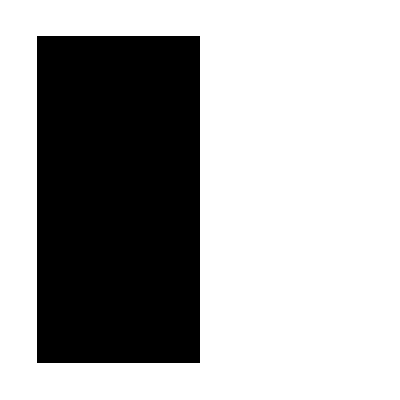
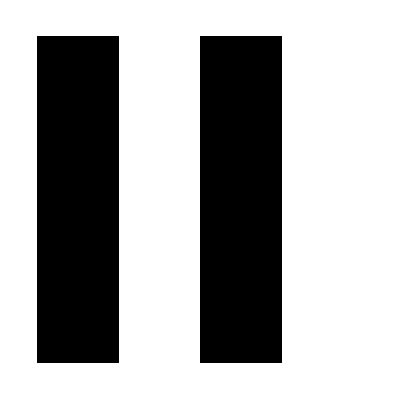
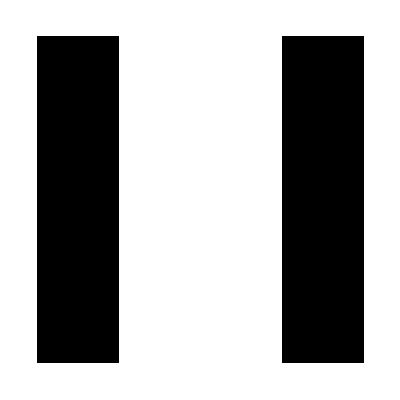
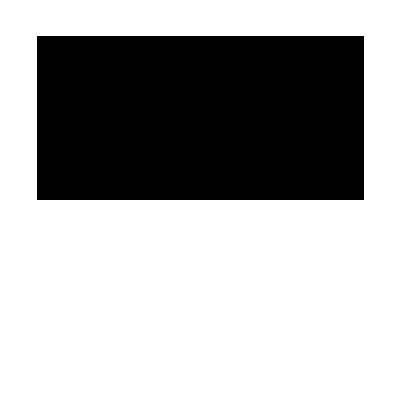
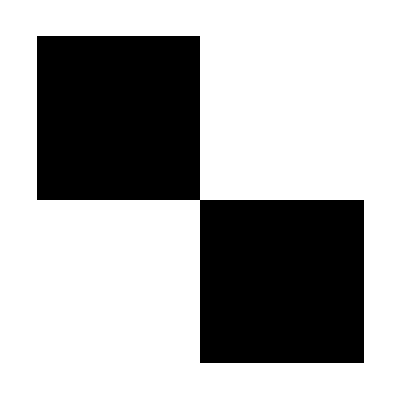
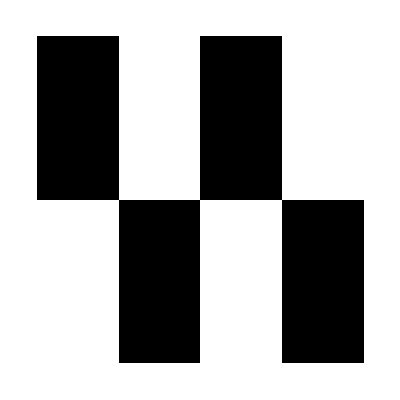
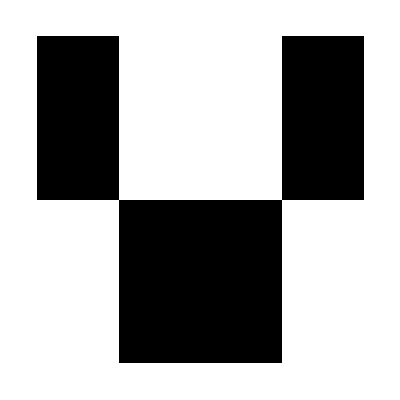
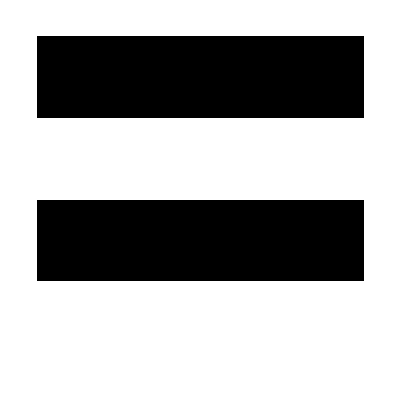

```mathematica
ArrayPlot/@twoQ[[2;;]]
```

```mathematica
KroneckerProduct[A,IdentityMatrix[4]]//MatrixForm
```

(1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1
1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | -1
1 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | -1
1 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 1)

```mathematica
KroneckerProduct[IdentityMatrix[4],A]//MatrixForm
```

(1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | -1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | -1 | 1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | -1 | -1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 1 | -1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | -1 | 1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | -1 | -1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | -1 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -1 | 1 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -1 | -1 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | -1 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -1 | 1 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -1 | -1 | 1)

```mathematica
(Binomial[15,3]-35)/28
```

15

```mathematica
15*16
```

240

```mathematica
KroneckerProduct[A,IdentityMatrix[4]].{1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0}
```

{2,2,2,2,2,2,2,2,0,0,0,0,0,0,0,0}

```mathematica
KroneckerProduct[IdentityMatrix[4],A].KroneckerProduct[A,IdentityMatrix[4]].{1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0}
```

{8,0,0,0,8,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
KroneckerProduct[IdentityMatrix[4],A].{1,1,0,0,0,0,1,1,0,0,0,0,0,0,0,0}
```

{2,2,0,0,2,-2,0,0,0,0,0,0,0,0,0,0}

```mathematica
diagonalOfGenerators=ArrayReshape[twoQ[[2;;]],{15,16}];
```

```mathematica
Flatten[Table[Table[MapThread[Times,{diagonalOfGenerators[[i]],diagonalOfGenerators[[j]]}],{j,15}],{i,15}],1]//Length
```

225

```mathematica
Binomial[15,2]
```

105

```mathematica
fourComp=MapThread[Times,{diagonalOfGenerators[[#[[1]]]],diagonalOfGenerators[[#[[2]]]]}]&/@Subsets[Range[15],{2}];fourComp//Tally
```

{{{1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0},3},{{1,1,0,0,1,1,0,0,0,0,0,0,0,0,0,0},3},{{1,0,0,0,1,0,0,0,0,1,0,0,0,1,0,0},3},{{1,1,0,0,0,0,0,0,1,1,0,0,0,0,0,0},3},{{1,0,0,0,0,1,0,0,1,0,0,0,0,1,0,0},3},{{1,1,0,0,0,0,0,0,0,0,0,0,1,1,0,0},3},{{1,0,0,0,0,1,0,0,0,1,0,0,1,0,0,0},3},{{1,0,1,0,1,0,1,0,0,0,0,0,0,0,0,0},3},{{1,0,0,0,1,0,0,0,0,0,1,0,0,0,1,0},3},{{1,0,1,0,0,0,0,0,1,0,1,0,0,0,0,0},3},{{1,0,0,0,0,0,1,0,1,0,0,0,0,0,1,0},3},{{1,0,1,0,0,0,0,0,0,0,0,0,1,0,1,0},3},{{1,0,0,0,0,0,1,0,0,0,1,0,1,0,0,0},3},{{1,0,0,1,1,0,0,1,0,0,0,0,0,0,0,0},3},{{1,0,0,0,1,0,0,0,0,0,0,1,0,0,0,1},3},{{1,0,0,1,0,0,0,0,1,0,0,1,0,0,0,0},3},{{1,0,0,0,0,0,0,1,1,0,0,0,0,0,0,1},3},{{1,0,0,1,0,0,0,0,0,0,0,0,1,0,0,1},3},{{1,0,0,0,0,0,0,1,0,0,0,1,1,0,0,0},3},{{1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0},3},{{1,1,0,0,0,0,1,1,0,0,0,0,0,0,0,0},3},{{1,0,1,0,0,1,0,1,0,0,0,0,0,0,0,0},3},{{1,0,0,1,0,1,1,0,0,0,0,0,0,0,0,0},3},{{1,1,0,0,0,0,0,0,0,0,1,1,0,0,0,0},3},{{1,1,0,0,0,0,0,0,0,0,0,0,0,0,1,1},3},{{1,0,0,0,0,1,0,0,0,0,1,0,0,0,0,1},3},{{1,0,0,0,0,1,0,0,0,0,0,1,0,0,1,0},3},{{1,0,1,0,0,0,0,0,0,1,0,1,0,0,0,0},3},{{1,0,0,0,0,0,1,0,0,1,0,0,0,0,0,1},3},{{1,0,1,0,0,0,0,0,0,0,0,0,0,1,0,1},3},{{1,0,0,0,0,0,1,0,0,0,0,1,0,1,0,0},3},{{1,0,0,1,0,0,0,0,0,1,1,0,0,0,0,0},3},{{1,0,0,0,0,0,0,1,0,1,0,0,0,0,1,0},3},{{1,0,0,0,0,0,0,1,0,0,1,0,0,1,0,0},3},{{1,0,0,1,0,0,0,0,0,0,0,0,0,1,1,0},3}}

```mathematica
Position[MapThread[Times,{diagonalOfGenerators[[#[[1]]]],diagonalOfGenerators[[#[[2]]]],diagonalOfGenerators[[#[[3]]]]}]&/@Subsets[Range[15],{3}],{1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0}]
```

{{2},{3},{4},{5},{14},{15},{16},{17},{27},{28},{37},{38},{92},{93},{94},{95},{104},{106},{115},{125},{170},{171},{182},{191},{236},{237},{246},{291}}

```mathematica
Subsets[Range[15],{3}][[{2,3,4,5,14,15,16,17,27,28,37,38,92,93,94,95,104,106,115,125,170,171,182,191,236,237,246,291}]]
```

{{1,2,4},{1,2,5},{1,2,6},{1,2,7},{1,3,4},{1,3,5},{1,3,6},{1,3,7},{1,4,6},{1,4,7},{1,5,6},{1,5,7},{2,3,4},{2,3,5},{2,3,6},{2,3,7},{2,4,5},{2,4,7},{2,5,6},{2,6,7},{3,4,5},{3,4,6},{3,5,7},{3,6,7},{4,5,6},{4,5,7},{4,6,7},{5,6,7}}

```mathematica
Binomial[15,2]/3
```

35

```mathematica
MapThread[Times,{diagonalOfGenerators[[#[[1]]]],diagonalOfGenerators[[#[[2]]]],diagonalOfGenerators[[#[[3]]]]}]&/@Subsets[Range[15],{3}]//Tally
```

{{{1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0},1},{{1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0},28},{{1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0},28},{{1,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0},28},{{1,1,0,0,1,1,0,0,0,0,0,0,0,0,0,0},1},{{1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},28},{{1,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0},28},{{1,0,0,0,1,0,0,0,0,1,0,0,0,1,0,0},1},{{1,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0},28},{{1,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0},28},{{1,1,0,0,0,0,0,0,1,1,0,0,0,0,0,0},1},{{1,0,0,0,0,1,0,0,1,0,0,0,0,1,0,0},1},{{1,1,0,0,0,0,0,0,0,0,0,0,1,1,0,0},1},{{1,0,0,0,0,1,0,0,0,1,0,0,1,0,0,0},1},{{1,0,1,0,1,0,1,0,0,0,0,0,0,0,0,0},1},{{1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0},28},{{1,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0},28},{{1,0,0,0,1,0,0,0,0,0,1,0,0,0,1,0},1},{{1,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0},28},{{1,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0},28},{{1,0,1,0,0,0,0,0,1,0,1,0,0,0,0,0},1},{{1,0,0,0,0,0,1,0,1,0,0,0,0,0,1,0},1},{{1,0,1,0,0,0,0,0,0,0,0,0,1,0,1,0},1},{{1,0,0,0,0,0,1,0,0,0,1,0,1,0,0,0},1},{{1,0,0,1,1,0,0,1,0,0,0,0,0,0,0,0},1},{{1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0},28},{{1,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0},28},{{1,0,0,0,1,0,0,0,0,0,0,1,0,0,0,1},1},{{1,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0},28},{{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1},28},{{1,0,0,1,0,0,0,0,1,0,0,1,0,0,0,0},1},{{1,0,0,0,0,0,0,1,1,0,0,0,0,0,0,1},1},{{1,0,0,1,0,0,0,0,0,0,0,0,1,0,0,1},1},{{1,0,0,0,0,0,0,1,0,0,0,1,1,0,0,0},1},{{1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0},1},{{1,1,0,0,0,0,1,1,0,0,0,0,0,0,0,0},1},{{1,0,1,0,0,1,0,1,0,0,0,0,0,0,0,0},1},{{1,0,0,1,0,1,1,0,0,0,0,0,0,0,0,0},1},{{1,1,0,0,0,0,0,0,0,0,1,1,0,0,0,0},1},{{1,1,0,0,0,0,0,0,0,0,0,0,0,0,1,1},1},{{1,0,0,0,0,1,0,0,0,0,1,0,0,0,0,1},1},{{1,0,0,0,0,1,0,0,0,0,0,1,0,0,1,0},1},{{1,0,1,0,0,0,0,0,0,1,0,1,0,0,0,0},1},{{1,0,0,0,0,0,1,0,0,1,0,0,0,0,0,1},1},{{1,0,1,0,0,0,0,0,0,0,0,0,0,1,0,1},1},{{1,0,0,0,0,0,1,0,0,0,0,1,0,1,0,0},1},{{1,0,0,1,0,0,0,0,0,1,1,0,0,0,0,0},1},{{1,0,0,0,0,0,0,1,0,1,0,0,0,0,1,0},1},{{1,0,0,0,0,0,0,1,0,0,1,0,0,1,0,0},1},{{1,0,0,1,0,0,0,0,0,0,0,0,0,1,1,0},1}}

```mathematica
Binomial[15,3]-(Binomial[7,3]-7)*15
```

35

```mathematica
Binomial[63,3]-(Binomial[7,3]-7)*651
```

21483

```mathematica
Subsets[Range[7],{3}]
```

{{1,2,3},{1,2,4},{1,2,5},{1,2,6},{1,2,7},{1,3,4},{1,3,5},{1,3,6},{1,3,7},{1,4,5},{1,4,6},{1,4,7},{1,5,6},{1,5,7},{1,6,7},{2,3,4},{2,3,5},{2,3,6},{2,3,7},{2,4,5},{2,4,6},{2,4,7},{2,5,6},{2,5,7},{2,6,7},{3,4,5},{3,4,6},{3,4,7},{3,5,6},{3,5,7},{3,6,7},{4,5,6},{4,5,7},{4,6,7},{5,6,7}}

```mathematica
Complement[Subsets[Range[7],{3}],Subsets[Range[15],{3}][[{2,3,4,5,14,15,16,17,27,28,37,38,92,93,94,95,104,106,115,125,170,171,182,191,236,237,246,291}]]]
```

{{1,2,3},{1,4,5},{1,6,7},{2,4,6},{2,5,7},{3,4,7},{3,5,6}}

```mathematica
PCEFigures[twoQ[[]]]
```

256

```mathematica
Binomial[15,3]
```

455

```mathematica
28*15
```

420

```mathematica
420/15
```

28

```mathematica
Binomial[7,3]
```

35

```mathematica
Binomial[15,3]
```

455

```mathematica
455*63
```

28665

```mathematica
440*63
```

27720

```mathematica
Binomial[63,3]-651-(Binomial[15,3]-15)*63
```

11340

```mathematica
38316-27720
```

10596

```mathematica
38316/651//N
```

58.8571

```mathematica
If[Total[Flatten[threeQ[[#]]][[1;;4]]]==4,#,Nothing]&/@Range[2,64]//Length
```

15

```mathematica
threeQ[[2]]//Flatten
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
Binomial[63,3]
```

39711

```mathematica
28*
```

28

```mathematica
diagThree=threeQ[[2;;]];
```

```mathematica
Tally[MapThread[Times,{diagThree[[#[[1]]]],diagThree[[#[[2]]]]}]&/@Subsets[Range[63],{2}]][[All,2]]
```

{3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3}

```mathematica
Tally[MapThread[Times,{diagThree[[#[[1]]]],diagThree[[#[[2]]]],diagThree[[#[[3]]]]}]&/@Subsets[Range[63],{3}]][[1;;3]]
```

{{{{{1,1,1,1},{1,1,1,1},{1,1,1,1},{1,1,1,1}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}},1},{{{{1,1,0,0},{1,1,0,0},{1,1,0,0},{1,1,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}},28},{{{{1,0,1,0},{1,0,1,0},{1,0,1,0},{1,0,1,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}},28}}

```mathematica
k=4;Length[If[Total[#[[1;;k]]]==k,#,Nothing]&/@KroneckerProduct[A,KroneckerProduct[A,A]]]-1
```

15

```mathematica
Binomial[7,3]
```

35

```mathematica
Binomial[15,4]-Binomial[7,4]*15
```

840

```mathematica
63*63
```

3969

```mathematica
k=2;If[Total[#[[1;;k]]]==k,#,Nothing]&/@KroneckerProduct[A,A]//Length
```

8

```mathematica
k=2;If[Total[#[[1;;k]]]==k,#,Nothing]&/@KroneckerProduct[A,KroneckerProduct[A,A]]//Length
```

32

```mathematica
Binomial[15,4]-15
```

1350

```mathematica
(Binomial[63,4]-35*1395)/(Binomial[15,4]-Binomial[7,4]*15)
```

651

```mathematica
(Binomial[255,4]-35*97155)/(Binomial[15,4]-Binomial[7,4]*15)
```

200787

```mathematica
(Binomial[1023,4]-35*6347715)/(Binomial[15,4]-Binomial[7,4]*15)
```

53743987

```mathematica
(Binomial[4095,4]-35*408345795)/(Binomial[15,4]-Binomial[7,4]*15)
```

13910980083

```mathematica
(Binomial[4^#-1,4]-35((Binomial[4^#-1,3]-Binomial[4^#-1,2]/3)/28))/(Binomial[15,4]-Binomial[7,4]*15)&/@Range[5]
```

{0,1,651,200787,53743987}

```mathematica
(Binomial[255,3]-10795)/28
```

97155

```mathematica
(Binomial[1023,3]-174251)/(Binomial[7,3]-7)
```

6347715

```mathematica
(Binomial[1023,4]-6347715)/(Binomial[15,4]-15)
```

168002857/5

```mathematica
Binomial[255,4]-97155
```

171964350

```mathematica
tally=Tally[MapThread[Times,{diagThree[[#[[1]]]],diagThree[[#[[2]]]],diagThree[[#[[3]]]],diagThree[[#[[4]]]]}]&/@Subsets[Range[63],{4}]];
```

```mathematica
(Binomial[63,4]-1395*35)/840
```

651

```mathematica
Binomial[15,4]-840
```

525

```mathematica
525/15
```

35

```mathematica
Tally[MapThread[Times,{diagThree[[#[[1]]]],diagThree[[#[[2]]]],diagThree[[#[[3]]]],diagThree[[#[[4]]]]}]&/@Subsets[Range[63],{4}]][[15;;20]]
```

{{{{{1,0,0,1},{0,1,1,0},{0,1,1,0},{1,0,0,1}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}},35},{{{{1,0,0,0},{1,0,0,0},{1,0,0,0},{1,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}},840},{{{{1,1,0,0},{1,1,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}},840},{{{{1,0,0,0},{1,0,0,0},{0,1,0,0},{0,1,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}},840},{{{{1,1,0,0},{0,0,0,0},{1,1,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}},840},{{{{1,0,0,0},{0,1,0,0},{1,0,0,0},{0,1,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}},840}}

```mathematica
840/35
```

24

```mathematica
(Binomial[63,3]-Binomial[63,2]/3)/28
```

1395

```mathematica
Binomial[4^#-1,2]/3&/@Range[10]
```

{1,35,651,10795,174251,2794155,44731051,715795115,11453115051,183251413675}

```mathematica
(Binomial[4^#-1,3]-Binomial[4^#-1,2]/3)/28&/@Range[10]
```

{0,15,1395,97155,6347715,408345795,26167664835,1675267338435,107225699266755,6862582190715075}

```mathematica
(Binomial[4^#-1,4]-35((Binomial[4^#-1,3]-Binomial[4^#-1,2]/3)/28))/840&/@Range[10]
```

{0,1,651,200787,53743987,13910980083,3571013994483,914807651274739,234230965858250739,59965700687947706355}

```mathematica
(Binomial[4^#-1,4]-35((Binomial[4^#-1,3]-Binomial[4^#-1,2]/3)/28))/(Binomial[15,4]-Binomial[7,4]*15)&/@Range[10]
```

{0,1,651,200787,53743987,13910980083,3571013994483,914807651274739,234230965858250739,59965700687947706355}

```mathematica
(Binomial[63,5]-651*651)/63
```

104842

```mathematica
Binomial[63,5]-315*651
```

6823782

```mathematica
35*Binomial[15,5]
```

105105

```mathematica
Binomial[31,5]
```

169911

```mathematica
Binomial[31,5]
```

169911

```mathematica
Binomial[15,4]
```

1365

```mathematica
1365-525
```

840

```mathematica
Binomial[7,4]-7
```

28

```mathematica
MapThread[Times,{diagonalOfGenerators[[#[[1]]]],diagonalOfGenerators[[#[[2]]]],diagonalOfGenerators[[#[[3]]]],diagonalOfGenerators[[#[[4]]]]}]&/@Subsets[Range[15],{4}]//Tally
```

{{{1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0},35},{{1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0},35},{{1,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0},35},{{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},840},{{1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},35},{{1,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0},35},{{1,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0},35},{{1,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0},35},{{1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0},35},{{1,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0},35},{{1,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0},35},{{1,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0},35},{{1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0},35},{{1,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0},35},{{1,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0},35},{{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1},35}}

```mathematica
Binomial[63,4]
```

595665

```mathematica
positions=Position[#,1]&/@(Diagonal/@PCEgenerators[3]);threeQubitGenerators=SparseArray[#->ConstantArray[1,32],{64}]&/@positions;
```

```mathematica
Q2G=SparseArray[Diagonal/@PCEgenerators[2]]
```

SparseArray[…]

```mathematica
SparseArray[MapThread[Times,{Q2G[[#[[1]]]],Q2G[[#[[2]]]],Q2G[[#[[3]]]],Q2G[[#[[4]]]]}]]&/@Subsets[Range[15],{4}]//Tally
```

{{SparseArray[…],35},{SparseArray[…],35},{SparseArray[…],35},{SparseArray[…],840},{SparseArray[…],35},{SparseArray[…],35},{SparseArray[…],35},{SparseArray[…],35},{SparseArray[…],35},{SparseArray[…],35},{SparseArray[…],35},{SparseArray[…],35},{SparseArray[…],35},{SparseArray[…],35},{SparseArray[…],35},{SparseArray[…],35}}

```mathematica
SparseArray[MapThread[Times,{Q2G[[#[[1]]]],Q2G[[#[[2]]]],Q2G[[#[[3]]]]}]]&/@Subsets[Range[15],{3}]//Tally
```

{{SparseArray[…],1},{SparseArray[…],28},{SparseArray[…],28},{SparseArray[…],28},{SparseArray[…],1},{SparseArray[…],28},{SparseArray[…],28},{SparseArray[…],1},{SparseArray[…],28},{SparseArray[…],28},{SparseArray[…],1},{SparseArray[…],1},{SparseArray[…],1},{SparseArray[…],1},{SparseArray[…],1},{SparseArray[…],28},{SparseArray[…],28},{SparseArray[…],1},{SparseArray[…],28},{SparseArray[…],28},{SparseArray[…],1},{SparseArray[…],1},{SparseArray[…],1},{SparseArray[…],1},{SparseArray[…],1},{SparseArray[…],28},{SparseArray[…],28},{SparseArray[…],1},{SparseArray[…],28},{SparseArray[…],28},{SparseArray[…],1},{SparseArray[…],1},{SparseArray[…],1},{SparseArray[…],1},{SparseArray[…],1},{SparseArray[…],1},{SparseArray[…],1},{SparseArray[…],1},{SparseArray[…],1},{SparseArray[…],1},{SparseArray[…],1},{SparseArray[…],1},{SparseArray[…],1},{SparseArray[…],1},{SparseArray[…],1},{SparseArray[…],1},{SparseArray[…],1},{SparseArray[…],1},{SparseArray[…],1},{SparseArray[…],1}}

```mathematica
SparseArray[MapThread[Times,{Q2G[[#[[1]]]],Q2G[[#[[2]]]],Q2G[[#[[3]]]],Q2G[[#[[4]]]],Q2G[[#[[5]]]]}]]&/@Subsets[Range[15],{5}]//Tally
```

{{SparseArray[…],21},{SparseArray[…],2688},{SparseArray[…],21},{SparseArray[…],21},{SparseArray[…],21},{SparseArray[…],21},{SparseArray[…],21},{SparseArray[…],21},{SparseArray[…],21},{SparseArray[…],21},{SparseArray[…],21},{SparseArray[…],21},{SparseArray[…],21},{SparseArray[…],21},{SparseArray[…],21},{SparseArray[…],21}}

```mathematica
15*21
```

315

```mathematica
erase[EigInfo_,PCEfrom_,invariantComponents_]:=Module[{dimPCE},
dimPCE=Length[Dimensions[PCEfrom][[2;;]]];
If[Count[#//Flatten,1]==invariantComponents,#,Nothing]&/@
DeleteDuplicates[
Flatten[
Table[
DeleteDuplicates[ReplacePart[PCEfrom[[i]]+#-ConstantArray[1,ConstantArray[4,dimPCE]],#->0&/@Position[PCEfrom[[i]]+#-ConstantArray[1,ConstantArray[4,dimPCE]],-1]]&/@EigInfo]
,{i,Length[PCEfrom]}]
,1]
];
MapThread[Times,{generators,PCEfrom}]
]
```

```mathematica
MapThread[Times,{generators,PCEfrom}]
```

```mathematica
Binomial[255,4]
```

172061505

```mathematica
97155*255
```

24774525